```mathematica
Off[General::"spell1"];
<<"SebaStuff`Rotations`"
<<"SebaStuff`ObjectsManipulation`"
<<"Utilities`FilterOptions`"
```

General::ivar: -2.99992 is not a valid variable.

General::ivar: -2.91829 is not a valid variable.

General::stop: Further output of General :: "ivar" will be suppressed during this calculation.

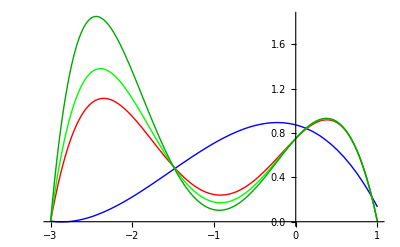

```mathematica
Clear[x,f,xi,i,ii,xpot];
r=1;
h=3;
points={{0,(r 3)/4},{r,0},Abs[x]/.Solve[2 x^2==1,x],{-h,0},{-h/2,r/2}};
xpot[ii_]:=Table[x^i,{i,0,ii}];
f[xi_,ii_:3]:=Fit[points,xpot[ii],x]/.x->xi;
Plot[{f[x,3],f[x,4],f[x,5],f[x,6]},{x,-h,r},PlotStyle->{Blue,Red,Green,Darker[Green]}]
```

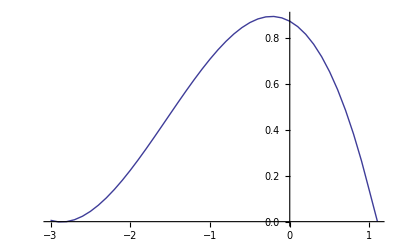

-Graphics3D-

```mathematica
Clear[x,f,xi,i,ii,xpot];
r=1;
h=3;
points={{0,(r 3)/4},{r,0},Abs[x]/.Solve[2 x^2==1,x],{-h,0},{-h/2,r/2}};
f[xi_]:=Fit[points,Table[x^i,{i,0,3}],x]/.x->xi;
rps=Table[{xa,f[xa]},{xa,-h,r,0.1}];
rps=Append[rps,{r+0.1,0}];
ListPlot[rps,Joined->True]
rps=(Append[#1,0]&)/@rps;
rps2=(Rotate3D[#1,0,90 °,0]&)/@rps;
rps3=(Rotate3D[#1,0,180 °,0]&)/@rps;
rps4=(Rotate3D[#1,0,-90 °,0]&)/@rps;
Show[Graphics3D[Polygon[rps]],Graphics3D[Polygon[rps2]],Graphics3D[Polygon[rps3]],Graphics3D[Polygon[rps4]]]
```

```mathematica
Clear[x,f,xi,i,w];
r=1;
h=3;
ppres=0.1;
wpres=15 °;
tpoints={{0,(r 3)/4},{r,0},Abs[x]/.Solve[2 x^2==1,x],{-h,0},{-h/2,r/2}};
f[xi_]:=Fit[tpoints,Table[x^i,{i,0,3}],x]/.x->xi;
rps=Table[{xa,f[xa]},{xa,-h,r,ppres}];
AppendTo[rps,{r,0}];
rps=(Append[#1,0]&)/@rps;
rpss=(RotateObject3D[rps,0,#1,0]&)/@Table[w,{w,0,360 °,wpres}];
Print["# of vertices: ",Plus@@(Length[#1]&)/@rpss];
Show[(Graphics3D[Polygon[#1]]&)/@rpss,Boxed->False]
```

# of vertices: 1050

-Graphics3D-

```mathematica
Clear[x,f,xi,i,w];
r=1;
h=3;
pprec=0.1;
wprec=15 °;
tpoints={{0,(r 3)/4},{r,0},Abs[x]/.Solve[2 x^2==r^2,x],{-h,0},{-h/2,r/2}};
f[xi_]:=Fit[tpoints,Table[x^i,{i,0,3}],x]/.x->xi;
rps=Table[{xa,f[xa],0},{xa,-h,r,pprec}];
AppendTo[rps,{r,0,0}];
rpss=(RotateObject3D[rps,0,#1,0]&)/@Table[w,{w,0,360 °,wprec}];
polies={};
For[i=1,i≠Length[rpss],++i,For[vi=1,vi≠Length[rpss⟦i⟧],++vi,AppendTo[polies,{rpss⟦i⟧⟦vi⟧,rpss⟦i⟧⟦vi+1⟧,rpss⟦i+1⟧⟦vi+1⟧,rpss⟦i+1⟧⟦vi⟧}]]];
Print["# of vertices: ",Plus@@(Length[#1]&)/@rpss];
Print["# of polygons: ",Plus@@(Length[#1]&)/@polies];
Show[(Graphics3D[Polygon[#1]]&)/@polies,Boxed->False,ViewPoint->{1,-1,2}]
```

# of vertices: 1050

# of polygons: 3936

-Graphics3D-

```mathematica
WaterDropHelper[r_,h_,pprec_]:=Module[{tpoints,x,f,rps,xa,i},Last[{tpoints={{0,(r 3)/4},{r,0},Abs[x]/.Solve[2 x^2==r^2,x],{-h,0},{-h/2,r/2}},f=Fit[tpoints,Table[x^i,{i,0,3}],x],rps=Table[{xa,f/.x->xa,0},{xa,-h,r,pprec}],Append[rps,{r,0,0}]}]];
WaterDrop[r_:1,h_:3,pprec_:0.1,wprec_:15 °]:=Module[{rps,rpss,polies={},w,i,vi},Last[{rps=WaterDropHelper[r,h,pprec],rpss=(RotateObject3D[rps,0,#1,0]&)/@Table[w,{w,0,360 °,wprec}],For[i=1,i≠Length[rpss],++i,For[vi=1,vi≠Length[rpss⟦i⟧],++vi,AppendTo[polies,{rpss⟦i⟧⟦vi⟧,rpss⟦i⟧⟦vi+1⟧,rpss⟦i+1⟧⟦vi+1⟧,rpss⟦i+1⟧⟦vi⟧}]]],polies}]];
PolygonWaterDrop[r_:1,h_:3,pprec_:0.1,wprec_:15 °]:=Module[{polies=WaterDrop[r,h,pprec,wprec]},(Polygon[#1]&)/@polies];
ShowWaterDrop[{r_:1,h_:3,pprec_:0.1,wprec_:15 °},opts___]:=Module[{polies=WaterDrop[r,h,pprec,wprec]},Show[(Graphics3D[Polygon[#1],Sequence@@FilterRules[Flatten[{opts}],Options[Graphics3D]]]&)/@polies,Sequence@@FilterRules[Flatten[{opts}],Options[Show]]]];
```

```mathematica
ShowWaterDrop[{},Boxed->False,ViewPoint->{1,-1,2}]
```

-Graphics3D-

```mathematica
Animate[Animate[Show[(Graphics3D[Polygon[#1]]&)/@RotateObject3D[WaterDrop[1,3,.5,30 °],w,0,w2],Boxed->False,ViewPoint->{0,-5,0}],{w,0 °,180 °,36 °}],{w2,0°,180°,36°}]
```